Parte 2 - BER da κ-μ

```mathematica
pdf[g_,gm_,k_,m_]:= (m(1+k)^((m +1)/2)g^((m -1)/2)Exp[-m(1+k)g/10^(gm/10)])/(k^((m -1)/2)Exp[m k](10^(gm/10))^((m +1)/2))BesselI[m -1,2 m √(k (k+1)g/10^(gm/10))];
probError[g_,alfa_]:=1/2 Exp[-alfa g];
```

```mathematica
BER[gm_, k_, m_, alfa_] := Re[Integrate[probError[g, alfa]×pdf[g, gm, k, m], {g,0,∞}]];
```

```mathematica
LogPlot[{BER[x,2,1,0.5],BER[x,2,2,0.5],BER[x,2,3,0.5],BER[x,2,4,0.5]},{x,-10,30},AxesLabel->{"γm (dB)","BER"},PlotRange->{10^-4,1},PlotLegends->{"μ=1","μ=2","μ=3","μ=4"}, PlotStyle->{Blue,Red,Green,Black}]
```

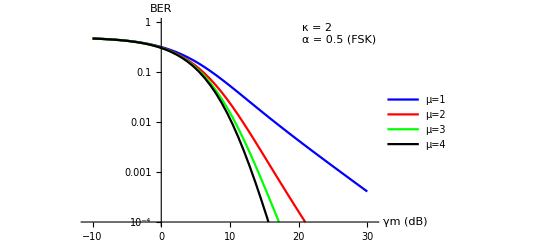

```mathematica
LogPlot[{BER[x,0.0001,2,0.5],BER[x,1,2,0.5],BER[x,2,2,0.5],BER[x,3,2,0.5]},{x,-10,30},AxesLabel->{"γm (dB)","BER"},PlotRange->{10^-4,1},PlotLegends->{"κ→0","κ=1","κ=2","κ=3"}, PlotStyle->{Blue,Red,Green,Black}]
```

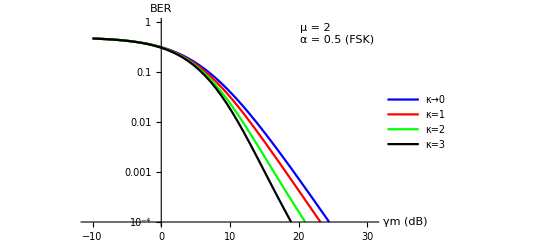

```mathematica
LogPlot[{BER[x,2,1,1],BER[x,2,2,1],BER[x,2,3,1],BER[x,2,4,1]},{x,-10,30},AxesLabel->{"γm (dB)","BER"},PlotRange->{10^-4,1},PlotLegends->{"μ=1","μ=2","μ=3","μ=4"}, PlotStyle->{Blue,Red,Green,Black}]
```

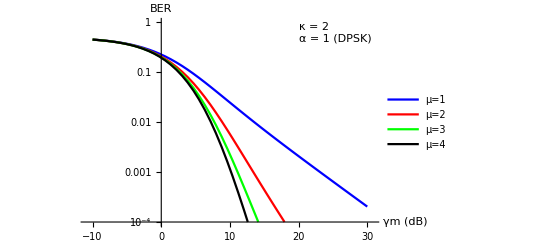

```mathematica
LogPlot[{BER[x,0.0001,2,1],BER[x,1,2,1],BER[x,2,2,1],BER[x,3,2,1]},{x,-10,30},AxesLabel->{"γm (dB)","BER"},PlotRange->{10^-4,1},PlotLegends->{"κ→0","κ=1","κ=2","κ=3"}, PlotStyle->{Blue,Red,Green,Black}]
```